```mathematica
ClearAll["Global`*"]
```

```mathematica
MeVdata‵20={#1*1000,1000*#2,#3,#4,#5}&@@@Import[NotebookDirectory[]<>"MeV-SFOPTbound-20TeV.csv"];
```

```mathematica
mSL21data=Select[MeVdata‵20,#[[1]]==21.&&#[[4]]>0&];
finetinedata={#1,#2,#4/#5}&@@@mSL21data;
finetunefunc[mSL_,sinθ_]:=Interpolation[finetinedata][mSL,sinθ]
```

```mathematica
mhpole=125.13;
v=246;
μS2[mS_,sinθ_]:=sinθ^2 mhpole^2+(1-sinθ^2)mS^2;
A[mS_,sinθ_]:=((mhpole^2-mS^2)sinθ √(1-sinθ^2))/v;
λhL[mS_,sinθ_]:=((1-sinθ^2)mhpole^2+sinθ^2 mS^2)/(2 v^2);
μSR[mSL_,sinθ_]:=finetunefunc[mSL,sinθ]μS2[mSL,sinθ]
```

```mathematica
Planckdata={#1,1000#2}&@@@Import[NotebookDirectory[]<>"./Planck.csv"];
Planckfunc[mSL_]:=Interpolation[Planckdata][mSL];
```

Interpolation::inhr: Requested order is too high; order has been reduced to {0,3}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {21,0.100002} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.54034} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {21,0.101053} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

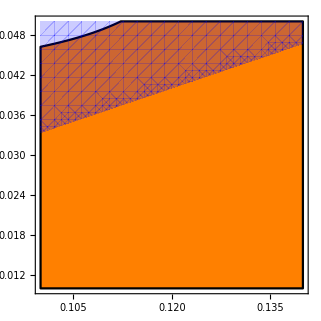

```mathematica
PlanckR=RegionPlot[sinθR<=Planckfunc[√μSR[21,sinθ]],{sinθ,0.1,0.14},{sinθR,0.01,0.05},PlotStyle->Directive[Orange,Opacity[0.2]],BoundaryStyle->None];
PlanckL=RegionPlot[sinθ<=Planckfunc[21],{sinθ,0.1,0.2},{sinθR,0.01,0.05}];
smallcorrection=RegionPlot[sinθ<3sinθR,{sinθ,0.1,0.14},{sinθR,0.01,0.05},PlotStyle->Directive
[Blue,Opacity[0.2]],BoundaryStyle->None];
Show[{PlanckL,PlanckR,smallcorrection},PlotRange->{{0.1,0.14},{0.01,0.05}}]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {0,3}.

General::stop: Further output of Interpolation::inhr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.0623} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.80488} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

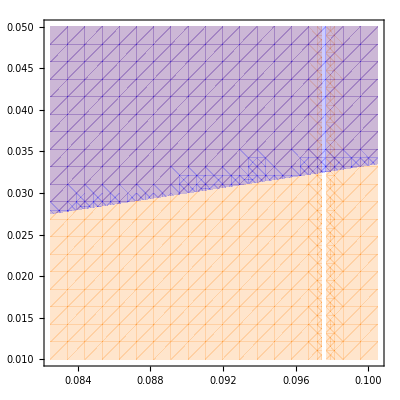

```mathematica
mSL15data=Select[MeVdata‵20,#[[1]]==15.&&#[[4]]>0&];
finetinedata={#1,#2,#4/#5}&@@@mSL15data;
finetunefunc[mSL_,sinθ_]:=Interpolation[finetinedata][mSL,sinθ]
mhpole=125.13;
v=246;
μS2[mS_,sinθ_]:=sinθ^2 mhpole^2+(1-sinθ^2)mS^2;
A[mS_,sinθ_]:=((mhpole^2-mS^2)sinθ √(1-sinθ^2))/v;
λhL[mS_,sinθ_]:=((1-sinθ^2)mhpole^2+sinθ^2 mS^2)/(2 v^2);
μSR[mSL_,sinθ_]:=finetunefunc[mSL,sinθ]μS2[mSL,sinθ]
PlanckR=RegionPlot[sinθR<=Planckfunc[√μSR[15,sinθ]],{sinθ,0.0825,0.1005},{sinθR,0.01,0.05},PlotStyle->Directive[Orange,Opacity[0.2]],BoundaryStyle->None];
PlanckL=RegionPlot[sinθ<=Planckfunc[15],{sinθ,0.0825,0.1005},{sinθR,0.01,0.05}];
smallcorrection=RegionPlot[sinθ<3sinθR,{sinθ,0.0825,0.1005},{sinθR,0.01,0.05},PlotStyle->Directive
[Blue,Opacity[0.2]],BoundaryStyle->None];
Show[{PlanckL,PlanckR,smallcorrection},PlotRange->{{0.0825,0.1005},{0.01,0.05}}]
```